#### gr. 1

Zad. 1

```mathematica
(* (a) *)
3/((x+1)(1-2x))//Apart
Sqrt[%]

(* (b) *)
y=(x^2-3x+1)/(x-1);
Limit[y,x->1,Direction->1]
Limit[y,x->1,Direction->-1]
a=Limit[y/x,x->Infinity]
b=Limit[y-a x,x->Infinity]
```

1/(1+x)-2/(-1+2 x)

√(1/(1+x)-2/(-1+2 x))

∞

-∞

1

-2

Zad. 2

```mathematica
f=4 x^5-3/x^4+5/x;
g=ArcTan[x]/3^x;
h=Sin[x^2]ArcSin[2x];
D[f,x]//Simplify
D[g,x]
D[h,x]//Simplify
```

(12-5 x^3+20 x^9)/x^5

3^-x/(1+x^2)-3^-x ArcTan[x] Log[3]

2 x ArcSin[2 x] Cos[x^2]+(2 Sin[x^2])/(√(1-4 x^2))

Zad. 3

(-7+6 x+x^2)/(3+x)^2

{{x→-7},{x→1}}

-7+6 x+x^2

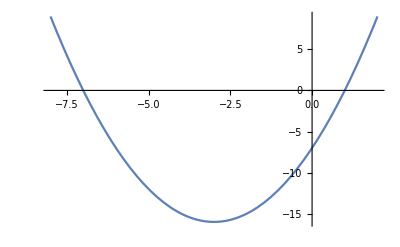

```mathematica
y=(x^2+7)/(x+3);
D[y,x]//Together
Solve[%==0,x]
Numerator[%%]
Plot[%,{x,-8,2}]
```

Zad. 4

```mathematica
Integrate[3/x^2-2/Sin[x]^2+4(x^2)^(1/3),x]
Integrate[Cos[x^3] x^2,x]
Integrate[x Cos[7x+5],x]
```

-3/x+12/5 x (x^2)^(1/3)+2 Cot[x]

Sin[x^3]/3

1/49 Cos[5+7 x]+1/7 x Sin[5+7 x]

Zad. 5

3+2 x-x^2

{{x→-1},{x→3}}

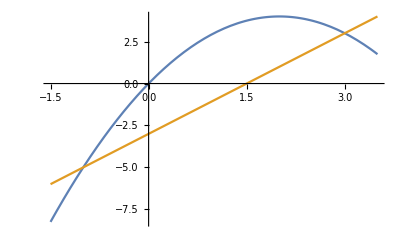

32/3

```mathematica
(x+1)(3-x)//Expand
y1=4x-x^2;
y2=2x-3;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-1.5,3.5}]
Integrate[y1-y2,{x,-1,3}]
```

Zad. 6

```mathematica
Clear[x,y,z];
z=x^3-x y+y^2-x+y;
D[z,x]
D[z,y]
pk=Solve[{%==0,%%==0},{x,y}]
Det[{{D[z,x,x],D[z,x,y]},{D[z,x,y],D[z,y,y]}}]
%/.pk
D[z,x,x]/.pk
```

-1+3 x^2-y

1-x+2 y

{{x→-1/3,y→-2/3},{x→1/2,y→-1/4}}

-1+12 x

{-5,5}

{-2,3}

#### gr. 2

Zad. 1

```mathematica
(* (a) *)
6/((x-2)(x+4))//Apart
Sqrt[%]

(* (b) *)
y=(-x^2+3)/(x+3);
Limit[y,x->-3,Direction->1]
Limit[y,x->-3,Direction->-1]
a=Limit[y/x,x->Infinity]
b=Limit[y-a x,x->Infinity]
```

1/(-2+x)-1/(4+x)

√(1/(-2+x)-1/(4+x))

∞

-∞

-1

3

Zad. 2

```mathematica
f=3/x^4+2(x^2)^(1/3);
g=Sin[x]/ArcSin[x];
h=(2x+1)^4 Cos[x^3];
D[f,x]//Simplify
D[g,x]//Simplify
D[h,x]//Simplify
h//TeXForm
```

-12/x^5+(4 x)/(3 (x^2)^(2/3))

(ArcSin[x] Cos[x]-Sin[x]/(√(1-x^2)))/ArcSin[x]^2

(1+2 x)^3 (8 Cos[x^3]-3 x^2 (1+2 x) Sin[x^3])

(2 x+1)^4 \cos \left(x^3\right)

Zad. 3

1+x-x^2-x^3

12 x+6 x^2-4 x^3-3 x^4

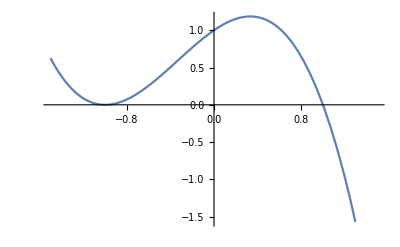

```mathematica
(x+1)^2(1-x)//Expand
Integrate[%,x]12//Expand
Plot[%%,{x,-1.5,1.5}]
```

Zad. 4

```mathematica
Integrate[3/(x^2+1)-5/x^3+1/((x^2)^(1/3)),x]
Integrate[x^4/((1+x^5)^10),x]
Integrate[Log[x]/x^3,x]
```

5/(2 x^2)+(3 x)/((x^2)^(1/3))+3 ArcTan[x]

-1/(45 (1+x^5)^9)

-1/(4 x^2)-Log[x]/(2 x^2)

Zad. 5

6-5 x+x^2

{{x→2},{x→3}}

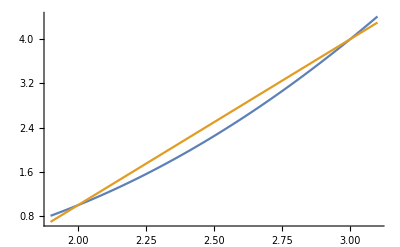

1/6

```mathematica
(x-2)(x-3)//Expand
y1=x^2-2x+1;
y2=3x-5;
Solve[y1==y2,x]
Plot[{y1,y2},{x,1.9,3.1}]
Integrate[y2-y1,{x,2,3}]
```

Zad. 6

```mathematica
z=x^2 y-x^2-2 y^2+6 x y;
D[z,x]
D[z,y]
pk=Solve[{%==0,%%==0},{x,y}]
Det[{{D[z,x,x],D[z,x,y]},{D[z,x,y],D[z,y,y]}}]
%/.pk
D[z,x,x]/.pk
```

-2 x+6 y+2 x y

6 x+x^2-4 y

{{x→-7,y→7/4},{x→-2,y→-2},{x→0,y→0}}

-28-24 x-4 x^2-8 y

{-70,20,-28}

{3/2,-6,-2}